# Investigating Quantum Interference Effects in Wolfram Models

Hatem Elshatlawy

Mentor: Max Piskunov

We examined quantum interference effects in WolframModels by reproducing the double-slit experiment in local and global multiway systems. We derived and evaluated a 1+1D double-slit interference using path integral formalism, constructed a quantum cellular automata (QCA) that emulates the double-slit experiment, and investigated various approaches for destructive interference in WolframModels.

## Wolfram Community Post

Mentor: Max Piskunov

We examined quantum interference effects in WolframModels by reproducing the double-slit experiment in local and global multiway systems. We derived and evaluated a 1+1D double-slit interference using path integral formalism, constructed a quantum cellular automata (QCA) that emulates the double-slit experiment, and investigated various approaches for destructive interference in WolframModels.

Interference between different branches in local multiway systems happens when two hyperedges that are branch-like separated are pulled into a single updated event (See figure below i.e.“Rule 3”).

A constructed toy-model of the double-slit system in local multiway system:

```mathematica
setup={{0,"s1"},{0,"s2"},{"s1","101"},{"101","e0"},{"s2","201"},{"201","e0"},{"s1","e1"},{"s2","211"},{"211","e1"},{"s2","e-1"},{"s1","2-11"},{"2-11","e-1"},{"o","o","e-1"},{"o","o","e0"},{"o","o","e1"}}
WolframModel[{{{0},{0,1}}->{{1,1,1}},{{0,0,0},{0,1}}->{{1}},{{"o","o","o"},{"o","o","s"},{"s","s","s"},{"s","s","s"}}->{{"o","o","o","s"}},{{"o","o","o"},{"o","o","s"},{"s"},{"s"}}->{{"o","o","o","s"}}},Join[{{0},{"o","o","o"}},setup],Infinity,"EventSelectionFunction"->None]["ExpressionsEventsGraph",VertexLabels->Placed[Automatic,After]]
```

{{0,s1},{0,s2},{s1,101},{101,e0},{s2,201},{201,e0},{s1,e1},{s2,211},{211,e1},{s2,e-1},{s1,2-11},{2-11,e-1},{o,o,e-1},{o,o,e0},{o,o,e1}}

-Graphics-

Whereas interference in global multiway-systems is obtained by applying a Knuth–Bendix completion algorithm.

A constructed toy-model of the double-slit system in global multiway system::

```mathematica
ResourceFunction["MultiwaySystem"][{"P"->"L","P"->"R","L"->"LL","R"->"RR"},"P",4,"StatesGraph"]
```

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"][{"P"->"L","P"->"R","L"->"LL","R"->"RR"},"CanonicalKnuthBendixCompletion"]
```

{L→R,R→L}

```mathematica
ResourceFunction["MultiwaySystem"][Join[{"P"->"L","P"->"R","L"->"LL","R"->"RR"},{"L"->"R","R"->"L"}],"P",4,"StatesGraph"]
```

-Graphics-

The new states obtained should then correspond to quantum interference effects between neighboring branches of the multiway system.

```mathematica
ResourceFunction["MultiwaySystem"][Join[{"P"->"L","P"->"R","L"->"LL","R"->"RR"},{"L"->"R","R"->"L"}],"P",4,"EvolutionCausalGraphStructure"]
```

-Graphics-

While interference in general is easy to obtain in both multiway systems, destructive interference is a bit more complicated! And to understand how destructive interference might fundamentally work in WolframModels we tried different approaches that will be discussed below.

Here’s a small demonstration of a two-slit diffraction pattern by a plane wave, where we get constructive interference that is when two amplitudes add up together, and destructive interference that is when two waves have the same amplitude but in opposite direction.

In the quantum version of the double-slit experiment, we also observe the same interference pattern as above by sending particles through a double-slit apparatus and that’s due to the quantum mechanical wave-like properties of matter. And so the distribution of the position of the particle at the end is something like this:

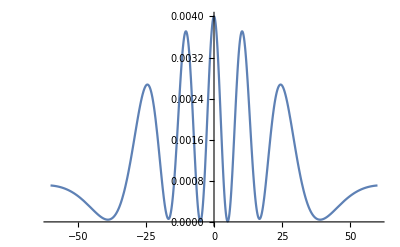

```mathematica
slit1={0,-10};
slit2={0,+10};
screenX=30;
With[{norm=Norm},Plot[Abs[ⅇ^(ⅈ norm[slit1-{screenX,y}])/norm[slit1-{screenX,y}]+ⅇ^(ⅈ norm[slit2-{screenX,y}])/norm[slit2-{screenX,y}]]^2,{y,-60,60}]]
```

Whereas the distribution for a single slit:

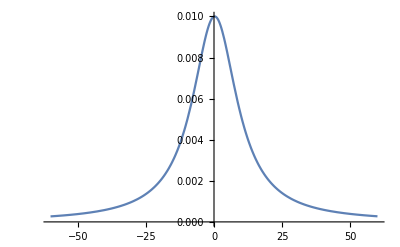

```mathematica
slit={0,1/4};
screenX=10;
With[{norm=Norm},Plot[Abs[ⅇ^(ⅈ norm[slit+{screenX,y}])/norm[slit-{screenX,y}]]^2,{y,-60,60}]]
```

So one way to obtain the quantum interference pattern in WolframModels is by constructing a system in ordinary physics and then implementing it in both local and global multiway systems, since the WolframModel is capable of universal computation, which means it can emulate any other system however complicated that may be.

#### Brute-force path-integral:

Our first approach was deriving a 1+1D double-slit interference using path integral formalism. The idea of path integrals is that if you have a photon (or any particle) in location A and want to work out its chance of moving to B, you imagine it taking every possible path between the two at the same time. All of these paths interfere with each other resulting in some final amplitude from which you can extract the probability of the particle moving from from A to B. Thus we consider the sum over all possible trajectories, where each path is equally likely, and thus contributes the same amount. Furthermore, the phase of this contribution at any given point along the path is determined by the action along the path:

A_path(x(t))= ⅇ^ⅈS

Where the action 𝒮 is defined as the integral of the Lagrangian: ∫ ℒ ⅆt

The differences in the cumulative action along the different paths (and thus the relative phases of the contributions) produces the interference pattern observed by the double-slit experiment.
All these contributions are then added together, and the magnitude of the final result is squared, to get the probability distribution for the position of the particle:

P(x(t))=Abs[ ∫_(all paths) ⅇ^ⅈS ]^2

We then compute the path integral for the relativistic case and the non-relativistic case.

Interference pattern for the relativistic case:

```mathematica
allTrajectories[start_,{t0_,t1_,dt_},ds_]:=Fold[Function[{trajectories,currentTime},Catenate[(Table[Append[#1,{currentTime,newPosition}],{newPosition,#1⟦-1,2⟧-dt,#1⟦-1,2⟧+dt,ds}]&)/@trajectories]],{{{t0,start}}},Range[t0+dt,t1,dt]]
```

A set of possible trajectories a particle can take

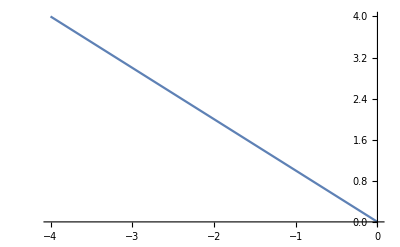
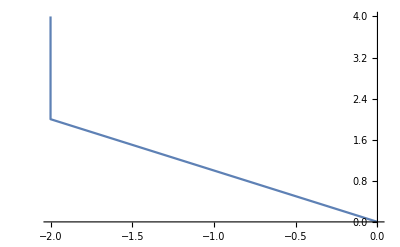
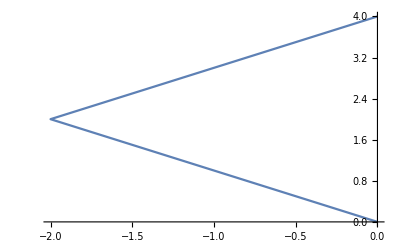
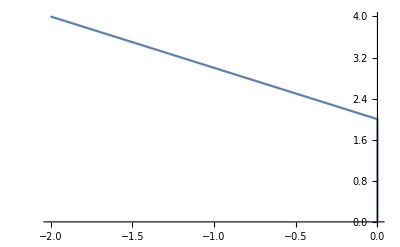
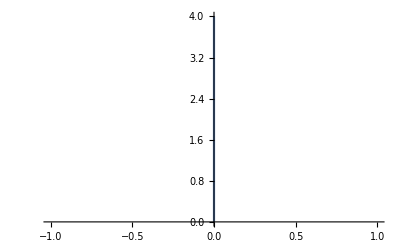
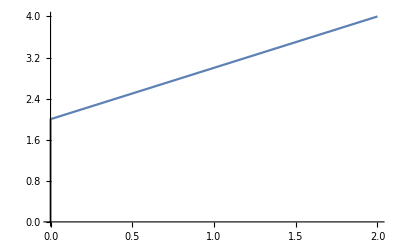
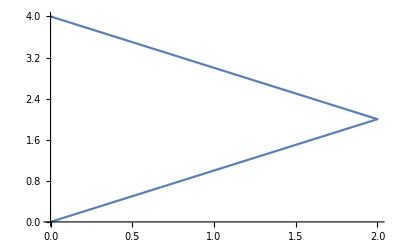
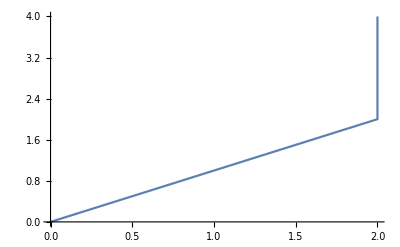

```mathematica
ListLinePlot/@Map[Reverse,allTrajectories[0,{0,5,2},2],{2}]
```

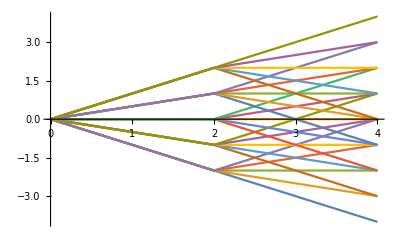

```mathematica
ListLinePlot[allTrajectories[0,{0,5,2},1]]
```

```mathematica
action[trajectory_,factor_]:=factor Total[(√((#1⟦2,1⟧-#1⟦1,1⟧)^2-(#1⟦2,2⟧-#1⟦1,2⟧)^2)&)/@Partition[trajectory,2,1]]
trajectoriesByFinalState[trajectories_]:=GroupBy[trajectories,#1⟦-1,2⟧&]
actionsByFinalState[trajectories_,factor_]:=Map[action[#1,factor]&,trajectoriesByFinalState[trajectories],{2}]
amplitudesByFinalState[trajectories_,factor_]:=Total/@Map[Exp[ⅈ #1]&,actionsByFinalState[trajectories,factor],{2}]
amplitudes=amplitudesByFinalState[trajectories];
```

```mathematica
With[{
amplitudes1=amplitudesByFinalState[allTrajectories[1,{0,6,1},1/4],10],
amplitudes2=amplitudesByFinalState[allTrajectories[-1,{0,6,1},1/4],10]},
ListLinePlot[Abs[Merge[{amplitudes1,amplitudes2},Total]]^2,PlotRange->All]]
```

The interference pattern we obtain:

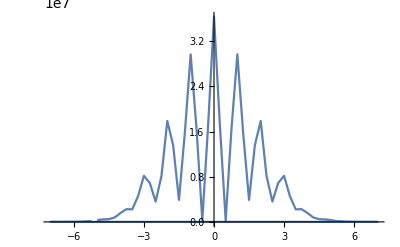

For the non-relativistic case:

```mathematica
allTrajectoriesNR[start_,{t0_,t1_,dt_},{s0_,s1_,ds_}]:=Fold[Function[{trajectoriesNR,currentTime},Catenate[Table[Append[#,{currentTime,newPosition}],{newPosition,s0,s1,ds}]&/@trajectoriesNR]],{{{t0,start}}},Range[t0+dt,t1,dt]]
```

```mathematica
actionNR[trajectoryNR_,factor_]:=factor Total[(#⟦2,2⟧-#⟦1,2⟧)^2/(#⟦2,1⟧-#⟦1,1⟧)&/@Partition[trajectoryNR,2,1]]
trajectoriesByFinalStateNR[trajectoriesNR_]:=GroupBy[trajectoriesNR,#⟦-1,2⟧&]
actionsByFinalStateNR[trajectoriesNR_,factor_]:=Map[actionNR[#,factor]&,trajectoriesByFinalStateNR[trajectoriesNR],{2}]
amplitudesByFinalStateNR[trajectoriesNR_,factor_]:=Total/@Map[Exp[ⅈ #]&,actionsByFinalStateNR[trajectoriesNR,factor],{2}]
```

#### Hamiltonian and unitary time-evolution operator:

Another approach is to construct a Quantum Cellular Automaton (QCA) that takes in a quantum state and evolve it using quantum operations to emulate the double-slit experiment, where we start with an initial Hamiltonian ℋ and evolve it using a time-evolution operator 𝒰.

```mathematica
𝒰=MatrixExp[-(ⅈ ℋ Δt)/ℏ]
```

Single-slit diffraction pattern:

```mathematica
hamiltonian1=Table[RotateRight[#,k],{k,0,99}]&@Join[{-2,1},ConstantArray[0,97],{1}];
dt1 = 1.*^-2;
init1=Join[Table[0,49],{1},Table[0,50]];
evolution1=Abs[NestList[MatrixExp[-ⅈ hamiltonian1 dt1].#&,init1,1000]]^2;
```

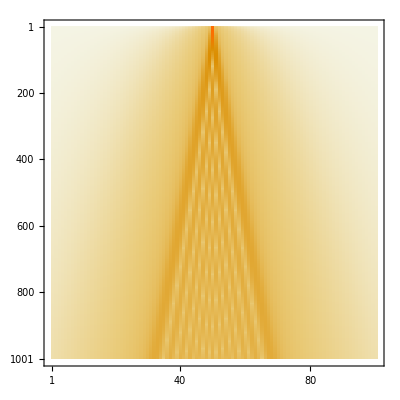

```mathematica
evolution1//(MatrixPlot[#,AspectRatio->1]&)
```

Double-slit interference pattern:

```mathematica
hamiltonian2=Table[RotateRight[#,k],{k,0,299}]&@Join[{-2,1},ConstantArray[0,297],{1}];
dt2=1.*^-1;
init2=Join[Table[0,149],{1},Table[0,150]];
evolution2=Abs[NestList[MatrixExp[-ⅈ hamiltonian2 dt2].#&,(RotateLeft[init2,50]+RotateRight[init2,50])/√2,600]]^2;
```

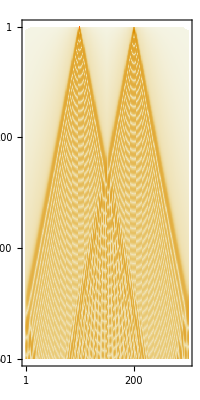

```mathematica
MatrixPlot[evolution2]
```

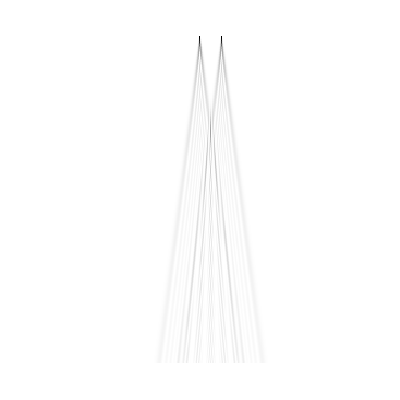

```mathematica
Abs[NestList[MatrixExp[ⅈ hamiltonian2 dt2].#&,(init2+RotateRight[init2,20])/√2,200]]^2//(ArrayPlot[#,AspectRatio->1]&)
```

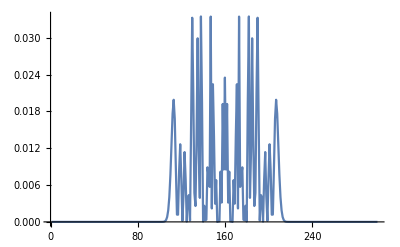

```mathematica
ListLinePlot[(Abs[NestList[MatrixExp[-ⅈ hamiltonian2 dt2].#&,(init2+RotateRight[init2,20])/√2,200]]^2)⟦200⟧,PlotRange->All]
```

It is shown in S. Wolfram’s technical introduction [1] how these models can emulate cellular automata, and so we can use the same construction to emulate this one here. However, it’s important to point out that this approach is unorthodox to the WolframModel, hence the spatial hypergraph wouldn’t correspond to space anymore.

#### Other approaches for destructive interference:

The following are some potential approaches to obtain destructive interference directly within WolframModels:

Perform a completion operation on two orthogonal states that are branchlike separated {A},{B} which will effectively treat them as a single equivalence class [A,B] so the information about which state contained A and which state contained B is lost, which implies no independent evolution of A and B.

```mathematica
ResourceFunction["MultiwaySystem"][{"S"->"A","S"->"B"},"S",3,"StatesGraph"]
```

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"][{"S"->"A","S"->"B","A"->"B","B"->"A"},"S",3,"StatesGraph","IncludeStateWeights"->True,VertexLabels->"VertexWeight"]
```

-Graphics-

Destructive interference would imply that there is an event {8}, existence of which prevents a branch of the evolution from happening  {6 → 7}

```mathematica
ResourceFunction["MultiwaySystem"][{"1"->"3","3"->"5","3"->"6","3"->"4","4"->"6","6"->"7"},"1",3,"StatesGraph"]
```

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"][{"1"->"3","1"->"8","3"->"5","3"->"6","3"->"4","4"->"6","8"->"6"},"1",3,"StatesGraph"]
```

-Graphics-

However this not possible in a non-overlapping or a local / global multiway system, because an evolution order exists in which the path {6 → 7} is evaluated.

Hence, true destructive interference as described above is not possible, and our only option is to make {6 → 7} vanishingly unlikely by creating a large number of alternative evolutions, starting from {8}.
In other words, we create so many new edges that imposes destructive interference, so that the original evolution path becomes unlikely.

Here we make many new edges from destructively-interfering ones (edges {4, 7} below) that the probability of using single edges is vanishingly small.

```mathematica
WolframModel[{{{1,2}}->{{2,3,4},{2,3,4},{2,3,4}},{{1,2}}->{{2,3,4,5},{2,3,4,5},{2,3,4,5}},{{2,3,4},{2,5,6,7}}->{{4,7}},{{2,3,4}}->{{2,3,4,5,6}}},{{1,2}},2,"EventSelectionFunction"->None]["ExpressionsEventsGraph",VertexLabels->Placed[Automatic,After]]
```

-Graphics-

A similar system in global multiway.

```mathematica
ResourceFunction["MultiwaySystem"][Join[{"12"->"234","12"->"2345","12"->"777","234"->"888","234"->"999","234"->"2567","2567"->"47"},{"234"->"2345","2345"->"234"}],"12",6,"EvolutionCausalGraphStructure"]
```

-Graphics-

### Future Work

Validate the conjecture that the new effective interference states that are obtained after applying a completion algorithm on a global multiway system are the same as the branchial-separated events that we could apply in the context of a local multiway system.

Optimize the destructive inference models.

Formulate a new interpretation of quantum mechanics

### Acknowledgment

Many thanks to Max Piskunov for his help, his advice, and for many stimulating deep discussions. 
I would like to extend my gratitude to J. Gorard and S. Wolfram.

### References

Stephen Wolfram, “A Class of Models with the Potential to Represent Fundamental Physics”

Jonathan Gorard, “Some Quantum Mechanical Properties of the Wolfram Model”

Max Piskunov, “Confluent Set Substitution Systems ", Wolfram Summer School 2019”

## Complete project work

Interference between different branches in local multiway systems happens when two hyperedges that are branch-like separated are pulled into a single updated event (See figure below i.e.“Rule 3”).

A constructed toy-model of the double-slit system in local multiway system:

```mathematica
setup={{0,"s1"},{0,"s2"},{"s1","101"},{"101","e0"},{"s2","201"},{"201","e0"},{"s1","e1"},{"s2","211"},{"211","e1"},{"s2","e-1"},{"s1","2-11"},{"2-11","e-1"},{"o","o","e-1"},{"o","o","e0"},{"o","o","e1"}}
WolframModel[{{{0},{0,1}}->{{1,1,1}},{{0,0,0},{0,1}}->{{1}},{{"o","o","o"},{"o","o","s"},{"s","s","s"},{"s","s","s"}}->{{"o","o","o","s"}},{{"o","o","o"},{"o","o","s"},{"s"},{"s"}}->{{"o","o","o","s"}}},Join[{{0},{"o","o","o"}},setup],Infinity,"EventSelectionFunction"->None]["ExpressionsEventsGraph",VertexLabels->Placed[Automatic,After]]
```

-Graphics-

Whereas interference in global multiway-systems is obtained by applying a Knuth–Bendix completion algorithm.

A constructed toy-model of the double-slit system in global multiway system::

```mathematica
ResourceFunction["MultiwaySystem"][{"P"->"L","P"->"R","L"->"LL","R"->"RR"},"P",4,"StatesGraph"]
```

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"][{"P"->"L","P"->"R","L"->"LL","R"->"RR"},"CanonicalKnuthBendixCompletion"]
```

{L→R,R→L}

```mathematica
ResourceFunction["MultiwaySystem"][Join[{"P"->"L","P"->"R","L"->"LL","R"->"RR"},{"L"->"R","R"->"L"}],"P",4,"StatesGraph"]
```

-Graphics-

The new states obtained should then correspond to quantum interference effects between neighboring branches of the multiway system.

```mathematica
ResourceFunction["MultiwaySystem"][Join[{"P"->"L","P"->"R","L"->"LL","R"->"RR"},{"L"->"R","R"->"L"}],"P",4,"EvolutionCausalGraphStructure"]
```

-Graphics-

While interference in general is easy to obtain in both multiway systems, destructive interference is a bit more complicated! And to understand how destructive interference might fundamentally work in WolframModels we tried different approaches that will be discussed below.

Here’s a small demonstration of a two-slit diffraction pattern by a plane wave, where we get constructive interference that is when two amplitudes add up together, and destructive interference that is when two waves have the same amplitude but in opposite direction.

```mathematica
Manipulate[Row[{DensityPlot[Cos[k Norm[{x,y}-d {0,2}]-f π t]/Norm[{x,y}-d {0,2}]+Cos[k Norm[{x,y}-d {0,-2}]-f π t]/Norm[{x,y}-d {0,-2}],{x,0,10},{y,-5,5},PlotPoints->50,ImageSize->300,PlotTheme->"Minimal"],Rotate[Plot[(200+Abs[-2 d+y]^2+Abs[2 d+y]^2+2 √((100+Abs[-2 d+y]^2) (100+Abs[2 d+y]^2)) Cos[k (√(100+Abs[-2 d+y]^2)-√(100+Abs[2 d+y]^2))])/(2 f (100+Abs[-2 d+y]^2) (100+Abs[2 d+y]^2)),{y,-5,5},ImageSize->280],-π/2]}],{t,0,15},{{f,5},1,10},{{k,5},1,10},{{d,1},0.5,3},SaveDefinitions->True]
```

In the quantum version of the double-slit experiment, we also observe the same interference pattern as above by sending particles through a double-slit apparatus and that’s due to the quantum mechanical wave-like properties of matter. And so the distribution of the position of the particle at the end is something like this:

```mathematica
slit1={0,-10};
slit2={0,+10};
screenX=30;
With[{norm=Norm},Plot[Abs[ⅇ^(ⅈ norm[slit1-{screenX,y}])/norm[slit1-{screenX,y}]+ⅇ^(ⅈ norm[slit2-{screenX,y}])/norm[slit2-{screenX,y}]]^2,{y,-60,60}]]
```

-Graphics-

Whereas the distribution for a single slit:

```mathematica
slit={0,1/4};
screenX=10;
With[{norm=Norm},Plot[Abs[ⅇ^(ⅈ norm[slit+{screenX,y}])/norm[slit-{screenX,y}]]^2,{y,-60,60}]]
```

-Graphics-

So one way to obtain the quantum interference pattern in WolframModels is by constructing a system in ordinary physics and then implementing that system in both local and global multiway systems, since the WolframModel is capable of universal computation, which means it can emulate any other system however complicated that may be.

#### Brute-force path-integral:

Our first approach was deriving a 1+1D double-slit interference using path integral formalism. The idea of path integrals is that if you have a photon (or any particle) in location A and want to work out its chance of moving to B, you imagine it taking every possible path between the two at the same time. All of these paths interfere with each other resulting in some final amplitude from which you can extract the probability of the particle moving from from A to B. Thus we consider the sum over all possible trajectories, where each path is equally likely, and thus contributes the same amount. Furthermore, the phase of this contribution at any given point along the path is determined by the action along the path:

A_path(x(t))= ⅇ^ⅈS

Where the action 𝒮 is defined as the integral of the Lagrangian: ∫ ℒ ⅆt

The differences in the cumulative action along the different paths (and thus the relative phases of the contributions) produces the interference pattern observed by the double-slit experiment.
All these contributions are then added together, and the magnitude of the final result is squared, to get the probability distribution for the position of the particle:

P(x(t))=Abs[ ∫_(all paths) ⅇ^ⅈS ]^2

We then compute the path integral for the relativistic case and the non-relativistic case.

Interference pattern for the relativistic case:

```mathematica
allTrajectories[start_,{t0_,t1_,dt_},ds_]:=Fold[Function[{trajectories,currentTime},Catenate[(Table[Append[#1,{currentTime,newPosition}],{newPosition,#1⟦-1,2⟧-dt,#1⟦-1,2⟧+dt,ds}]&)/@trajectories]],{{{t0,start}}},Range[t0+dt,t1,dt]]
```

A set of possible trajectories a particle can take

```mathematica
ListLinePlot/@Map[Reverse,allTrajectories[0,{0,5,2},2],{2}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListLinePlot[allTrajectories[0,{0,5,2},1]]
```

-Graphics-

```mathematica
action[trajectory_,factor_]:=factor Total[(√((#1⟦2,1⟧-#1⟦1,1⟧)^2-(#1⟦2,2⟧-#1⟦1,2⟧)^2)&)/@Partition[trajectory,2,1]]
trajectoriesByFinalState[trajectories_]:=GroupBy[trajectories,#1⟦-1,2⟧&]
actionsByFinalState[trajectories_,factor_]:=Map[action[#1,factor]&,trajectoriesByFinalState[trajectories],{2}]
amplitudesByFinalState[trajectories_,factor_]:=Total/@Map[Exp[ⅈ #1]&,actionsByFinalState[trajectories,factor],{2}]
amplitudes=amplitudesByFinalState[trajectories];
```

```mathematica
With[{
amplitudes1=amplitudesByFinalState[allTrajectories[1,{0,6,1},1/4],10],
amplitudes2=amplitudesByFinalState[allTrajectories[-1,{0,6,1},1/4],10]},
ListLinePlot[Abs[Merge[{amplitudes1,amplitudes2},Total]]^2,PlotRange->All]]
```

The interference pattern we obtain:

-Graphics-

For the non-relativistic case:

```mathematica
allTrajectoriesNR[start_,{t0_,t1_,dt_},{s0_,s1_,ds_}]:=Fold[Function[{trajectoriesNR,currentTime},Catenate[Table[Append[#,{currentTime,newPosition}],{newPosition,s0,s1,ds}]&/@trajectoriesNR]],{{{t0,start}}},Range[t0+dt,t1,dt]]
```

```mathematica
actionNR[trajectoryNR_,factor_]:=factor Total[(#⟦2,2⟧-#⟦1,2⟧)^2/(#⟦2,1⟧-#⟦1,1⟧)&/@Partition[trajectoryNR,2,1]]
trajectoriesByFinalStateNR[trajectoriesNR_]:=GroupBy[trajectoriesNR,#⟦-1,2⟧&]
actionsByFinalStateNR[trajectoriesNR_,factor_]:=Map[actionNR[#,factor]&,trajectoriesByFinalStateNR[trajectoriesNR],{2}]
amplitudesByFinalStateNR[trajectoriesNR_,factor_]:=Total/@Map[Exp[ⅈ #]&,actionsByFinalStateNR[trajectoriesNR,factor],{2}]
```

#### Hamiltonian and unitary time-evolution operator:

Another approach is to construct a Quantum Cellular Automaton (QCA) that takes in a quantum state and evolve it using quantum operations to emulate the double-slit experiment, where we start with an initial Hamiltonian ℋ and evolve it using a time-evolution operator 𝒰.

```mathematica
𝒰=MatrixExp[-(ⅈ ℋ Δt)/ℏ]
```

Single-slit diffraction pattern:

```mathematica
hamiltonian1=Table[RotateRight[#,k],{k,0,99}]&@Join[{-2,1},ConstantArray[0,97],{1}];
dt1 = 1.*^-2;
init1=Join[Table[0,49],{1},Table[0,50]];
evolution1=Abs[NestList[MatrixExp[-ⅈ hamiltonian1 dt1].#&,init1,1000]]^2;
```

```mathematica
evolution1//(MatrixPlot[#,AspectRatio->1]&)
```

-Graphics-

Double-slit interference pattern:

```mathematica
hamiltonian2=Table[RotateRight[#,k],{k,0,299}]&@Join[{-2,1},ConstantArray[0,297],{1}];
dt2=1.*^-1;
init2=Join[Table[0,149],{1},Table[0,150]];
evolution2=Abs[NestList[MatrixExp[-ⅈ hamiltonian2 dt2].#&,(RotateLeft[init2,50]+RotateRight[init2,50])/√2,600]]^2;
```

```mathematica
MatrixPlot[evolution2]
```

-Graphics-

```mathematica
Abs[NestList[MatrixExp[ⅈ hamiltonian2 dt2].#&,(init2+RotateRight[init2,20])/√2,200]]^2//(ArrayPlot[#,AspectRatio->1]&)
```

-Graphics-

```mathematica
ListLinePlot[(Abs[NestList[MatrixExp[-ⅈ hamiltonian2 dt2].#&,(init2+RotateRight[init2,20])/√2,200]]^2)⟦200⟧,PlotRange->All]
```

-Graphics-

It is shown in S. Wolfram’s technical introduction [1] how these models can emulate cellular automata, and so we can use the same construction to emulate this one here. However, it’s important to point out that this approach is unorthodox to the WolframModel, hence the spatial hypergraph wouldn’t correspond to space anymore.

#### Other approaches for destructive interference:

The following are some potential approaches to obtain destructive interference directly within WolframModels:

Perform a completion operation on two orthogonal states that are branchlike separated {A},{B} which will effectively treat them as a single equivalence class [A,B] so the information about which state contained A and which state contained B is lost, which implies no independent evolution of A and B.

```mathematica
ResourceFunction["MultiwaySystem"][{"S"->"A","S"->"B"},"S",3,"StatesGraph"]
```

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"][{"S"->"A","S"->"B","A"->"B","B"->"A"},"S",3,"StatesGraph","IncludeStateWeights"->True,VertexLabels->"VertexWeight"]
```

-Graphics-

Destructive interference would imply that there is an event {8}, existence of which prevents a branch of the evolution from happening  {6 → 7}

```mathematica
ResourceFunction["MultiwaySystem"][{"1"->"3","3"->"5","3"->"6","3"->"4","4"->"6","6"->"7"},"1",3,"StatesGraph"]
```

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"][{"1"->"3","1"->"8","3"->"5","3"->"6","3"->"4","4"->"6","8"->"6"},"1",3,"StatesGraph"]
```

-Graphics-

However this not possible in a non-overlapping or a local / global multiway system, because an evolution order exists in which the path {6 → 7} is evaluated.

Hence, true destructive interference as described above is not possible, and our only option is to make {6 → 7} vanishingly unlikely by creating a large number of alternative evolutions, starting from {8}.
In other words, we create so many new edges that imposes destructive interference, so that the original evolution path becomes unlikely.

Here we make many new edges from destructively-interfering ones (edges {4, 7} below) that the probability of using single edges is vanishingly small.

```mathematica
WolframModel[{{{1,2}}->{{2,3,4},{2,3,4},{2,3,4}},{{1,2}}->{{2,3,4,5},{2,3,4,5},{2,3,4,5}},{{2,3,4},{2,5,6,7}}->{{4,7}},{{2,3,4}}->{{2,3,4,5,6}}},{{1,2}},2,"EventSelectionFunction"->None]["ExpressionsEventsGraph",VertexLabels->Placed[Automatic,After]]
```

-Graphics-

A similar system in global multiway.

```mathematica
ResourceFunction["MultiwaySystem"][Join[{"12"->"234","12"->"2345","12"->"777","234"->"888","234"->"999","234"->"2567","2567"->"47"},{"234"->"2345","2345"->"234"}],"12",6,"EvolutionCausalGraphStructure"]
```

-Graphics-

### Future Work

Validate the conjecture that the new effective interference states that are obtained after applying a completion algorithm on a global multiway system are the same as the branchial-separated events that we could apply in the context of a local multiway system.

Optimize the destructive inference models.

Formulate a new interpretation of quantum mechanics

### Acknowledgment

Many thanks to Max Piskunov for his help, his advice, and for many stimulating deep discussions. 
I would like to extend my gratitude to J. Gorard and S. Wolfram.

### References

Stephen Wolfram, “A Class of Models with the Potential to Represent Fundamental Physics”

Jonathan Gorard, “Some Quantum Mechanical Properties of the Wolfram Model”

Max Piskunov, “Confluent Set Substitution Systems ", Wolfram Summer School 2019”